```mathematica
Пример 3
```

```mathematica
sigma=2;
cappa=0.5;
cc=5;
u[x_,t_]:=If[x>=cc t,0,(sigma (cc /cappa) (cc t-x))^(1/sigma)]
```

```mathematica
xcomp=Table[x,{x,0,10,0.2}];
```

```mathematica
dataIm=Import["D:\\6 семестр\\Методы вычислений\\LR_2_new-master\\LR_2\\OUTPUT\\example3Im.txt","Data"];
```

```mathematica
dataMix=Import["D:\\6 семестр\\Методы вычислений\\LR_2_new-master\\LR_2\\OUTPUT\\example3MixP.txt","Data"];
```

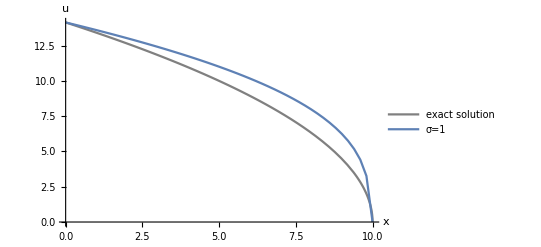

```mathematica
tt=20000 0.0001;
Show[Plot[(sigma cc/cappa (cc tt-xx))^(1/sigma),{xx,0,10},AxesLabel->{"x","u"},PlotStyle->Gray,PlotLegends->{"exact solution"}],ListLinePlot[Transpose[{xcomp,dataIm[[-1]]}],PlotLegends->{"σ=1"}]]
```

```mathematica
Пример 0
```

```mathematica
u[x_,t_,lambda_]:=Sin[π x] Exp[- lambda t];
```

```mathematica
data0Ex=Import["D:\\6 семестр\\Методы вычислений\\LR_2_new-master\\LR_2\\OUTPUT\\example0Ex8.txt","Table"];
```

```mathematica
data0Im=Import["D:\\6 семестр\\Методы вычислений\\LR_2_new-master\\LR_2\\OUTPUT\\example0Im.txt","Data"];
```

```mathematica
data0Mix=Import["D:\\6 семестр\\Методы вычислений\\LR_2_new-master\\LR_2\\OUTPUT\\example0Mix8.txt","Data"];
```

```mathematica
xcomp=Table[x,{x,0,1,0.1}];
```

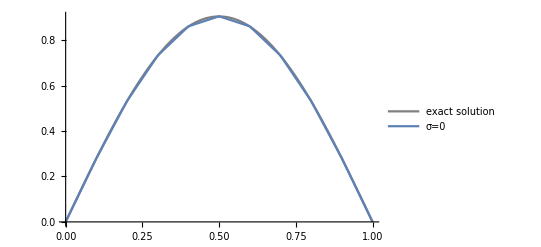

```mathematica
Show[Plot[u[xx,0.1,1],{xx,0,1},PlotLegends->{"exact solution"},PlotStyle->Gray],ListLinePlot[Transpose[{xcomp,data0Ex[[-1]]}],PlotLegends->{"σ=0"}]]
```

```mathematica
gif=Table[ListLinePlot[data0Im[[tt]],PlotRange->{{0,Length[data0Im[[1]]]+1},{-1,1}},AxesLabel->{"x","u"}],{tt,1,Length[data0Im],10}];
```

```mathematica
Export["D:\\6 семестр\\Методы вычислений\\LR_2_new-master\\Отчет\\data0Ex.gif",gif]
```

D:\6 семестр\Методы вычислений\LR_2_new-master\Отчет\data0Ex.gif

```mathematica
Порядок для примера 0
```

```mathematica
uu=Table[u[xx,0.1,1],{xx,0,1,0.1}]
```

{0.,0.27961,0.53185,0.732029,0.860552,0.904837,0.860552,0.732029,0.53185,0.27961,1.10811×10^-16}

```mathematica
n1=Norm[data0Ex[[-1]]-Table[u[xx,0.1,1],{xx,0,1,0.1}]]
```

0.00155974

```mathematica
n2=Norm[data0Ex[[-1]]-Table[u[xx,0.1,1],{xx,0,1,0.1/2}]]
```

0.000552722

```mathematica
n3=Norm[data0Ex[[-1]]-Table[u[xx,0.1,1],{xx,0,1,0.1/4}]]
```

0.000195585

```mathematica
n4=Norm[data0Ex[[-1]]-Table[u[xx,0.1,1],{xx,0,1,0.1/8}]]//N
```

0.000069615

```mathematica
n2/n1
```

0.354367

```mathematica
Log[2,%]
```

-1.49668

```mathematica
Пример 1
```